```mathematica
Clear["Global`*"]
```

```mathematica
(*Base Cases*)
win[4,_]=1;
win[_,3]=0;
```

```mathematica
Pstrike[b_,s_]:=Pstrike[b,s]=(win[b,1+s]-win[1+b,s])/(-4 p+win[b,1+s]+p win[b,1+s]-win[1+b,s]);
```

```mathematica
Pball[b_,s_]:=Pball[b,s]=1-Pstrike[b,s];
Pswing[b_,s_]:=Pstrike[b,s];
```

```mathematica
Pwait[b_,s_]:=Pball[b,s];
```

```mathematica
win[b_,s_]:=win[b,s]=Simplify[Pstrike[b,s] (4p+(1-p) win[b,s+1])+(1-Pstrike[b,s]) win[b,s+1]];
```

```mathematica
(*Base Cases for probability at vertex*)
```

```mathematica
P[0,0]=1;
P[_,-1]=0;
P[-1,_]=0;
```

```mathematica
P[b_,s_]:=P[b,s]=Simplify[P[b-1,s] (Pball[b-1,s]*Pwait[b-1,s])+P[b,s-1] (Pball[b,s-1]Pswing[b,s-1]+Pstrike[b,s-1]Pwait[b,s-1]+Pstrike[b,s-1]Pswing[b,s-1](1-p))];
```

```mathematica
NumberForm[N[Maximize[{P[3,2],0<=p<=1},p],10]]
```

{0.2959679934,{p→0.2269732325}}

General::munfl: 0.0000204286^66 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^67 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^68 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

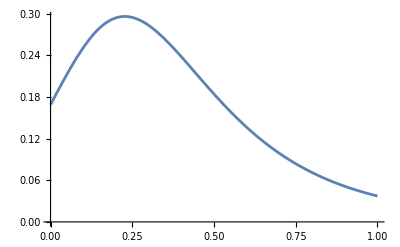

```mathematica
Plot[P[3,2],{p,0,1}]
```

```mathematica
(*Solve for strike probability at indifference and swing probability (they're the same)*)
```

```mathematica
Solve[a(4p+(1-p)w[b,s+1])+(1-a)w[b,s+1]==a w[b,s+1]+(1-a)w[b+1,s],a]
```

{{a→(w[b,1+s]-w[1+b,s])/(-4 p+w[b,1+s]+p w[b,1+s]-w[1+b,s])}}

```mathematica
Solve[sw(4p+(1-p)w[b,s+1])+(1-sw)w[b,s+1]==sw w[b,s+1]+(1-sw)w[b+1,s],sw]
```

{{sw→(w[b,1+s]-w[1+b,s])/(-4 p+w[b,1+s]+p w[b,1+s]-w[1+b,s])}}